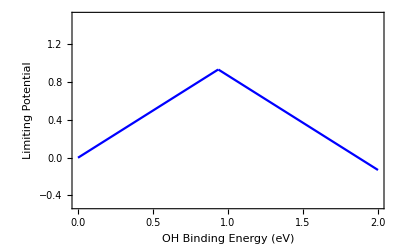

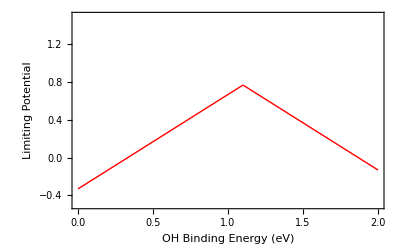

```mathematica
Emolh2o=-14.21;
Emolh2=-6.75;
Emolo2=-9.85;
Emolh2o2=-18.13984949;

TSh2o=0.67;
ZPEh2o=0.56;
TSh2=0.41;
ZPEh2=0.27;
ZPEo=0.1;
ZPEoh=0.3;
TSo2=0.64;
ZPEo2=0.1;
ZPEooh=0.4;
TSh2o2=0.71996809;
ZPEh2o2=0.74;

soloh=-0.6;
solooh=-0.23;

Eo=2Eoh;
Eooh=Eoh+3.2;

G1=Eooh-Emolo2+2*Emolh2o-2*Emolh2;
G2=Eo-Eooh;
G3=Eoh-Eo;
G4=-Eoh;
G=Max[G1,G2,G3,G4];

G1h2o2=Eooh-Emolo2+2*Emolh2o-2*Emolh2;
G2h2o2=Emolh2o2-Eooh+Emolh2-2*Emolh2o;
Gh2o2=Max[G1h2o2,G2h2o2];

volcano=Plot[-G,{Eoh,0,2},Frame->True,FrameStyle->Directive[Thick,Black,18],Axes->{False,False,False},PlotRange->{-0.5,1.5},PlotStyle->Blue,FrameLabel->{Style["OH Binding Energy (eV)",Large,Black],Style["Limiting Potential",Large,Black]},FrameTicksStyle->Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],FrameStyle->Thick]

volcanoh2o2=Plot[-Gh2o2,{Eoh,0,2},Frame->True,FrameStyle->Directive[Thick,Black,18],Axes->{False,False,False},PlotRange->{-0.5,1.5},PlotStyle->{Red,Thick},FrameLabel->{Style["OH Binding Energy (eV)",Large,Black],Style["Limiting Potential",Large,Black]},FrameTicksStyle->Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->18],FrameStyle->Thick]
```